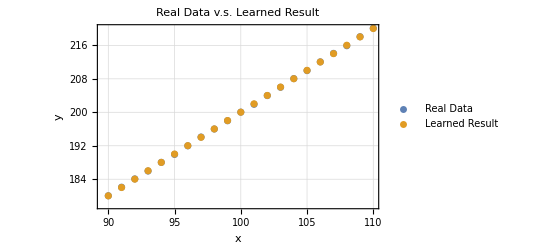

```mathematica
ClearAll["Global`*"];
(* Store the neural network to a wlnet file *)
storePath=FileNameJoin[{NotebookDirectory[],"trained_net.wlnet"}];
n=100;(* Data size *)
x=Range[n];(* Generate Simple Input *)
(* Linear output with little noise *)
y=2x+RandomReal[{-0.1,0.1},n];
(* A linear layer with scalar input and scalar output *)
l=NetInitialize@LinearLayer[1,"Input"->1];
(* Use NetExtract to get the Weights and Biases *)
(* NetExtract[l,{1,"Weights"}] *)

(* The data should be like {{x1}->{y1},{x2}->{y2}} *)
r=NetTrain[l,Map[List,Thread[x->y],{2}]];
(* Store the trained data to a file *)
Export[storePath,r];

(* Generate more data *)
newX=Range[n+1,2n];
newY=2newX+RandomReal[{-0.1,0.1},n];
(* Restore the previously trained network *)
l=Import[storePath];
(* Train it again.
 Stop Criterion should be absolute change of Loss not 
  exceed in given times (Patience).
 ValidationSet means randomly sample 10% of data
  to avoid overfitting.
 This train should be very fast.*)
r=NetTrain[l,Thread[(List/@newX)->(List/@newY)],
TrainingStoppingCriterion->
<|"Criterion"->"Loss","Patience"->5,
"AbsoluteChange"->0.001|>,
ValidationSet->Scaled[0.1]];

(* Let's Plot the Results! *)
finalX=Range[n-10,n+10];
finalY=Join[y,newY]⟦finalX⟧;
ListPlot[Transpose/@{{finalX,finalY},{finalX,r[List/@finalX]//Flatten}},
PlotLabel->"Real Data v.s. Learned Result",
Frame->True,
FrameLabel->{"x","y"},
PlotLegends->Placed[LineLegend[{"Real Data","Learned Result"},
LegendFunction->(Framed[#1,FrameMargins->0]&)],
{Left,Top}],
GridLines->Automatic]
```